```mathematica
(*--- Biophysical model of reverse blebbing ---*)
(*--- Modified on 30/07/2019 ---*)
Clear[cf,Plysis,θ,sol,sol2,eqsol,f];
SetDirectory["/Users/cairola/Dropbox (The Francis Crick)/ChiuFanShared/Project-Glaucoma/paper"];
date=DateString[{"Year","_","Month","_","Day"}];
If[DirectoryQ[date]==False,CreateDirectory[date]];
SetDirectory[date];
SetOptions[Style,FontFamily->"Arial"];

TimeConvert[x_]:=Module[{time,result,days,hours,minutes,seconds,format},With[{dy=86400,hr=3600,mn=60},days=Floor[time/dy];time=x;
time=Mod[time,dy];
hours=Floor[time/hr];
minutes=Floor[Mod[time,hr]/mn];
seconds=Floor[time-hr*hours-mn*minutes]];
format=IntegerString[#,10,2]&;
If[days>0,StringJoin[Riffle[format/@{hours,minutes,seconds},{":"}]," +",IntegerString[days]," days"],StringJoin[Riffle[format/@{hours,minutes,seconds},{":"}]]]]

(*--- Fixed parameters ---*)
cf=0.0075;

(*--- Plot specs ---*)
Size=20;imgSize=600;imagePadding={{100,100},{80,10}};
dashsty=Directive[Dashed,AbsoluteThickness[1]];
mdefault=Directive[Black,AbsoluteThickness[2]];
tdefault=Directive[DotDashed,Black,AbsoluteThickness[2]];
cdefault=Directive[Darker[RGBColor[0,154,0,255]],AbsoluteThickness[2]];
cshaded=Directive[Lighter[Darker[RGBColor[0,154,0,255]],0.45],Opacity[0.3],AbsoluteThickness[2]];
mshaded=Directive[Lighter[Black,0.65],Opacity[0.3],AbsoluteThickness[2]];
tshaded=Directive[Lighter[Black,0.65],Opacity[0.3],DotDashed,AbsoluteThickness[2]];
bfont=Directive[Size,Black,FontFamily->"Arial"];
SetOptions[Plot,PlotRange->All];
SetOptions[ListPlot,PlotRange->All,Joined->True];
SetOptions[ListLogPlot,PlotRange->All,Joined->True];

(*--- Equilibrium solutions ---*)
Clear[sol,sol2,sol3,eqsol];
(*--- Numerical Algorithms ---*)
θ[xm_,y_]:={ArcSin[xm/y],π-ArcSin[xm/y]};
area[r_,R_,ϕ_,xm_,xE_]:=2π r^2(1-Cos[ϕ])+π (xE^2-xm^2);

(*--- A. Vacuole: Cortex dominated phase ; Cell: Cortex dominated phase ---*)
sol[p_,n_]:=Module[{x0,aC,xm,xE,gM,tC,k1,k2,counter,y,ϕ,rC,Γ0,Α0,Α,s,s0,ΓV,ΓC,rL,x1,x2,rV,z,i,pC,j,R},R={};
x0=r0[[n]];aC=αC[[n]];xm=rm[[n]];xE=rE[[n]];
gM=γM[[n]];tC=ΤC[[n]];
(*--- A.1 Set angle ---*)
For[j=1,j≤2,j++,
Clear[y,x1,x2,rV,rC,ΓV,ΓC,z];
(*--- A.2 Initialise parameters ---*)
k1=1;k2=1;counter=0;
ϕ=Part[θ[xm,y],j];rC=(x0^3+2 y^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
Γ0=gM+tC;Α0=4π x0^2-π xE^2;s0=π xE^2;
Α=3π rC^2-π xE^2;s=2π y^2(1-Cos[ϕ])+π (xE^2-xm^2);
ΓV=Γ0;ΓC=Γ0;
(*--- A.3 Numerical solutions ---*)
rL=y/.NSolve[y^2+3(2 y^3+x0^3)^(2/3)==3 x0^2(1+aC)&&y>0,y]; Clear[y];
x1=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];Clear[y];
x2=Re[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 x0}]]];Clear[y];
(*--- A.3.1 Check solutions ---*)
While[Abs[x1-x2]<10^-2&&counter<10,k1/=10;counter+=1;
x1=First[Re[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]]; Clear[y];
];
(*--- A.3.2 Set solutions ---*)
rV=Re[{x1,x2}];ϕ=Re[ϕ/.{y->rV}];
rC=Re[rC/.{y->rV}];z=(2ΓC)/rC;
(*--- A.3.3 Check validity of numerical results ---*)
For[i=1,i<=Length[rV],i++,
(*Print[StringJoin["Check rV[[",ToString[i],"]]=",ToString[rV[[i]]]]];*)
If[rV[[i]]<0,rV=Drop[rV,{i}]; rC=Drop[rC,{i}];z=Drop[z,{i}];ϕ=Drop[ϕ,{i}]; i-=1,
pC=ΓC/rC[[i]]+ΓV/rV[[i]];
If[Abs[pC-p/2]>10^-2,
(*Print[StringJoin["pC=",ToString[ScientificForm[pC,2]]]];
Print[StringJoin["p/2=",ToString[ScientificForm[p/2,2]]]];
Print[StringJoin["ΔP=",ToString[ScientificForm[Abs[pC-p/2],2]]]];*)
rV=Drop[rV,{i}]; rC=Drop[rC,{i}];z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1;
];
];
];
(*--- A.4 Print results ---*)
For[i=1,i<=Length[rV],i++,AppendTo[R,{rV[[i]],rC[[i]],z[[i]],ΓV,ΓC,ϕ[[i]]}]];
];
R=DeleteDuplicates[R,First@#1==First@#2 &];Return[R]
];

(*--- B. Vacuole: Membrane dominated phase ; Cell: Cortex dominated phase ---*)
sol2[p_,n_]:=Module[{x0,aC,xm,xE,gM,Σ0,tC,β,k1,k2,counter,y,ϕ,rC,Γ0,Α0,Α,ΑC,s,s0,sC,ΓV,ΓC,rL,x1,x2,rV,z,i,pC,j,R},R={};
x0=r0[[n]];aC=αC[[n]];xm=rm[[n]];xE=rE[[n]];
gM=γM[[n]];tC=ΤC[[n]];β=b[[n]];
Α0=3π x0^2-π xE^2;s0=π xE^2;sC=s0(1+aC);
(*--- B.1 Set angle ---*)
For[j=1,j≤2,j++,
Clear[y,x1,x2,rV,rC,ΓV,ΓC,z];
(*--- B.2 Initialise parameters ---*)
k1=10;k2=1;counter=0;
Γ0=gM+tC;Σ0=gM+tC;
ϕ=Part[θ[xm,y],j];rC=(x0^3+2 y^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
Α=3π rC^2-π xE^2;s=2π y^2(1-Cos[ϕ])+(π xE^2-π xm^2);
ΓV=Σ0+β(Exp[(s-sC)/sC]-1);ΓC=Γ0;
(*--- B.3 Numerical solutions ---*)
rL=y/.NSolve[y^2+3(2 y^3+x0^3)^(2/3)==3 x0^2(1+aC)&&y>0,y];Clear[y];
x1=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]];
(*--- B.3.1 Check solutions ---*)
While[Abs[x1-x2]<10^-2&&counter<10,k2/=10;counter+=1;
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]]; Clear[y];
];
(*--- B.3.2 Set solutions ---*)
rV=Sort[Re[{x1,x2}]];ϕ=Re[ϕ/.{y->rV}];
rC=Re[rC/.{y->rV}];
ΓV=Re[ΓV/.{y->rV}];z=(2ΓC)/rC;
(*--- B.3.3 Check validity of numerical results ---*)
For[i=1,i<=Length[rV],i++,
(*Print[StringJoin["Check rV[[",ToString[i],"]]=",ToString[rV[[i]]]]];*)
If[rV[[i]]<0,rV=Drop[rV,{i}]; rC=Drop[rC,{i}]; ΓV=Drop[ΓV,{i}];z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1,
pC=ΓC/rC[[i]]+ΓV[[i]]/rV[[i]];
If[Abs[pC-p/2]>10^-2,
(*Print[StringJoin["pC=",ToString[ScientificForm[pC,2]]]];
Print[StringJoin["p/2=",ToString[ScientificForm[p/2,2]]]];
Print[StringJoin["ΔP=",ToString[ScientificForm[Abs[pC-p/2],2]]]];*)
rV=Drop[rV,{i}];rC=Drop[rC,{i}];ΓV=Drop[ΓV,{i}];
z=Drop[z,{i}];ϕ=Drop[ϕ,{i}]; i-=1;
];
];
];
(*--- B.4 Print results ---*)
For[i=1,i<=Length[rV],i++,AppendTo[R,{rV[[i]],rC[[i]],z[[i]],ΓV[[i]],ΓC,ϕ[[i]]}]];
];
R=DeleteDuplicates[R,First@#1==First@#2 &];
Return[R]
];

(*--- C. Membrane dominated phase ---*)
sol3[p_,n_]:=Module[{x0,aC,xm,xE,gM,Σ0,tC,β,k1,k2,counter,y,ϕ,rC,Γ0,Α0,Α,ΑC,s,s0,sC,ΓV,ΓC,rL,x1,x2,rV,z,i,pC,j,R},R={};
x0=r0[[n]];aC=αC[[n]];xm=rm[[n]];xE=rE[[n]];
gM=γM[[n]];tC=ΤC[[n]];β=b[[n]];
Α0=3π x0^2-π xE^2;s0=π xE^2;
ΑC=Α0(1+aC);sC=s0(1+aC);
(*--- C.1 Set angle ---*)
For[j=1,j≤2,j++,
Clear[y,x1,x2,rV,rC,ΓV,ΓC,z];
(*--- C.2 Initialise parameters ---*)
k1=10;k2=1;counter=0;
Γ0=gM+tC;Σ0=gM+tC;
ϕ=Part[θ[xm,y],j];rC=(x0^3+2 y^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
Α=3π rC^2-π xE^2;s=2π y^2(1-Cos[ϕ])+π(xE^2-xm^2);
ΓV=Σ0+β(Exp[(s-sC)/sC]-1);ΓC=Γ0+β(Exp[(Α-ΑC)/ΑC]-1);
(*--- C.3 Numerical solutions ---*)
rL=y/.NSolve[y^2+3(2 y^3+x0^3)^(2/3)==3 x0^2(1+aC)&&y>0,y];Clear[y];
x1=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]];
(*--- C.3.1 Check solutions ---*)
While[Abs[x1-x2]<10^-2&&counter<10,k2/=10;counter+=1;
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]]; Clear[y];
];
(*--- C.3.2 Set solutions ---*)
rV=Sort[Re[{x1,x2}]];ϕ=Re[ϕ/.{y->rV}];
rC=Re[rC/.{y->rV}];ΓC=Re[ΓC/.{y->rV}];
ΓV=Re[ΓV/.{y->rV}];z=(2ΓC)/rC;
(*--- C.3.3 Check validity of numerical results ---*)
For[i=1,i<=Length[rV],i++,
(*Print[StringJoin["Check rV[[",ToString[i],"]]=",ToString[rV[[i]]]]];*)
If[rV[[i]]<0,rV=Drop[rV,{i}]; rC=Drop[rC,{i}]; ΓV=Drop[ΓV,{i}];ΓC=Drop[ΓC,{i}]; z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1,
pC=ΓC[[i]]/rC[[i]]+ΓV[[i]]/rV[[i]];
If[Abs[pC-p/2]>10^-2,
(*Print[StringJoin["pC=",ToString[ScientificForm[pC,2]]]];
Print[StringJoin["p/2=",ToString[ScientificForm[p/2,2]]]];
Print[StringJoin["ΔP=",ToString[ScientificForm[Abs[pC-p/2],2]]]];*)
rV=Drop[rV,{i}];rC=Drop[rC,{i}];ΓV=Drop[ΓV,{i}];
ΓC=Drop[ΓC,{i}];z=Drop[z,{i}];ϕ=Drop[ϕ,{i}]; i-=1;
];
];
];
(*--- B.4 Print results ---*)
For[i=1,i<=Length[rV],i++,AppendTo[R,{rV[[i]],rC[[i]],z[[i]],ΓV[[i]],ΓC[[i]],ϕ[[i]]}]];
];
R=DeleteDuplicates[R,First@#1==First@#2 &];
Return[R]
];

(*--- Lysis pressure ---*)
αl=0.05;
Plysis[n_]:=Module[{x0,aC,xm,xE,R,ΑC,ΑM,gM,tC,Δs,β},
x0=r0[[n]];aC=αC[[n]];xm=rm[[n]];xE=rE[[n]];
gM=γM[[n]];tC=ΤC[[n]];β=b[[n]];
ΑC=(π xE^2)(1+aC); ΑM=(1+αl)ΑC; 
R=gM+tC+β( Exp[((ΑM-ΑC)/ΑC)]-1);
Return[R];]

(*--- C. Equilibrium solutions ---*)
eqsol[p_,n_]:=Module[{s1,s2,s3,sF,Α,Α0,s,s0,rC,rV,xE,r1,r2,r3,r4,xC,z,ϕ,i,xm,x0,aC},sF={};
xm=rm[[n]];x0=r0[[n]];aC=αC[[n]];xE=rE[[n]];
Α0=3π x0^2-π xE^2;s0=π xE^2;
(*--- A. Vacuole: Cortex dominated phase ; Cell: Cortex dominated phase ---*)
s1=sol[p,n];
For[i=1,i≤Length[s1],i++,
rV=Part[s1[[i]],1];rC=Part[s1[[i]],2]; ϕ=Part[s1[[i]],6];
Α=3π rC^2-π xE^2;s=2π rV^2(1-Cos[ϕ])+(π xE^2-π xm^2);
If[Α≤Α0(1+aC)&&s≤s0(1+aC),AppendTo[sF,s1[[i]]];];
];
(*--- B. Vacuole: Membrane dominated phase ; Cell: Cortex dominated phase ---*)
s2=sol2[p,n];(*Print[s2];*)
For[i=1,i≤Length[s2],i++,
rV=Part[s2[[i]],1];rC=Part[s2[[i]],2]; ϕ=Part[s2[[i]],6];
Α=3π rC^2-π xE^2;s=2π rV^2(1-Cos[ϕ])+(π xE^2-π xm^2);
If[s≥s0(1+aC) && Α≤Α0(1+aC),AppendTo[sF,s2[[i]]];];
];
(*--- C. Vacuole: Membrane dominated phase ; Cell: Membrane dominated phase ---*)
s3=sol3[p,n];
For[i=1,i≤Length[s3],i++,
rV=Part[s3[[i]],1];rC=Part[s3[[i]],2]; ϕ=Part[s3[[i]],6];
Α=3π rC^2-π xE^2;s=2π rV^2(1-Cos[ϕ])+(π xE^2-π xm^2);
If[s≥s0(1+aC) &&Α≥Α0(1+aC),AppendTo[sF,s3[[i]]];];
];
(*--- Final solution ---*)
sF=Select[sF,Length[#]==6&];
Return[sF]
];


(*--- Linear stability analysis ---*)
d[p_,n_]:=Module[{z,xm,x0,xE,aC,β,e,s1,s2,rV,rC,ΓS,ΓC,ΓE,ϕ,Α,Α0,ΑC,s,s0,sC,δR,i,Γ0},
xm=rm[[n]];xE=rE[[n]];x0=r0[[n]]; aC=αC[[n]];
β=b[[n]];ΓE=ΕC[[n]];Γ0=γM[[n]]+ΤC[[n]];
Α0=3π x0^2-π xE^2;ΑC=Α0(1+aC);
s0=π xE^2;sC=s0(1+aC);
(*--- A. Compute solution ---*)
s1=eqsol[p,n];z={};
If[Length[s1]==0,Clear[z],
For[i=1,i≤Length[s1],i++,
s2=Part[s1,i];
(*--- B. Compute thickness ---*)
rV=s2[[1]];rC=s2[[2]];ΓS=s2[[4]];ΓC=s2[[5]];ϕ=s2[[6]];
If[rV≥xm && ϕ>π/2,
δR=1/4(rV/rC)^2(1-Cos[ϕ])^2(2+Cos[ϕ]+2(1+Cos[ϕ])^2/Abs[Cos[ϕ]]);
AppendTo[z,AppendTo[s2,Γ0/(2ΓE)(1-rV^2/rC^2 δR)]];
];
];
];
Return[z];
]
```

```mathematica
(*--- Function to generate the phase diagram ---*)
Clear[engine,manager];
(*--- Perfusion pressure drop ---*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
p1=0.1;p2=4000;P=1500;
ρ=logspace[Log10[p1],Log10[p2],P];
p1=cf;p2=4000cf;

(*--- Phase diagram generator ---*)
engine[n_]:=Module[{force,j},
SetSharedVariable[j];
force=Monitor[ParallelTable[j=Length[ρ]-m;
{ρ[[m]],d[ρ[[m]],n]},{m,1,Length[ρ]}],j];
Return[force]
]

(*--- Data analysis ---*)
manager[n_]:=Module[{force,pdiag,results,x0,s0,a,xm,xE,β,gM,tC,e,h,Δs,aC,p,tab0,tab1,tab2,tab3,
row1,col1,row2,col2,row3,col3,dat1,dat2,dat3,Tdat1,Mdat1,Cdat1,Tdat2,Mdat2,Cdat2,Tdat3,Mdat3,Cdat3,Tdat,Mdat,Cdat,fCdat,fMdat,fTdat,table},

(*--- Output of parameters ---*)
PrintTemporary[StringJoin["--- ",ToString[n]," ---"]];
Export[stream1,StringJoin["--- Parameters set ",ToString[n]," ---\n"]];
x0=r0[[n]];Export[stream1,StringJoin["x0=",ToString[x0],"\n"]];
xm=rm[[n]];Export[stream1,StringJoin["a=",ToString[xm],"\n"]];
xE=rE[[n]]; Export[stream1,StringJoin["rE=",ToString[xE],"\n"]];s0=π xE^2;
aC=αC[[n]];Export[stream1,StringJoin["αC=",ToString[aC],"\n"]];
β=b[[n]];Export[stream1,StringJoin["b=",ToString[β],"\n"]];
gM=γM[[n]];Export[stream1,StringJoin["γM=",ToString[gM],"\n"]];
tC=ΤC[[n]];Export[stream1,StringJoin["ΤC=",ToString[tC],"\n"]];
e=ΕC[[n]];Export[stream1,StringJoin["ΕC=",ToString[e],"\n"]];
h=hC[[n]];Export[stream1,StringJoin["hC=",ToString[h],"\n"]];
p=Plysis[n];Export[stream1,StringJoin["Plysis=",ToString[p],"\n"]];
Export[stream1,StringJoin["--- End ---\n"]];


(*--- Generate data---*)
PrintTemporary["--- Running engine ---"];
pdiag=engine[n];
PrintTemporary["--- End ---"];

(*--- Subdivide data ---*)
Export[stream1,"--- Data table ---\n"];
tab0=Select[pdiag,Length[Part[#,2]]==0&];
tab1=Select[pdiag,Length[Part[#,2]]==1&];Export[stream1,StringJoin["Length tab1=",ToString[Length[tab1]],"\n"]];
row1=tab1[[All,1]];col1=Flatten[tab1[[All,2]],1];
tab2=Select[pdiag,Length[Part[#,2]]==2&];Export[stream1,StringJoin["Length tab2=",ToString[Length[tab2]],"\n"]];
row2=tab2[[All,1]];col2=tab2[[All,2]];
tab3=Select[pdiag,Length[Part[#,2]]==3&];Export[stream1,StringJoin["Length tab3=",ToString[Length[tab3]],"\n"]];
row3=tab3[[All,1]];col3=tab3[[All,2]];


PrintTemporary["--- Manage data ---"];

(*--- Manage data ---*)
dat1=Table[{row1[[m]] cf,col1[[m,1]],col1[[m,2]],col1[[m,3]]cf,col1[[m,4]],col1[[m,5]],col1[[m,6]],col1[[m,7]]},{m,1,Length[row1]}];
dat2=Table[{row2[[m]] cf,col2[[m,l,1]],col2[[m,l,2]],col2[[m,l,3]]cf,col2[[m,l,4]],col2[[m,l,5]],col2[[m,l,6]],col2[[m,l,7]]},{m,1,Length[row2]},{l,1,2}];
dat3=Table[{row3[[m]] cf,col3[[m,l,1]],col3[[m,l,2]],col3[[m,l,3]]cf,col3[[m,l,4]],col3[[m,l,5]],col3[[m,l,6]],col3[[m,l,7]]},{m,1,Length[row3]},{l,1,3}];

(*--- Rearrange data ---*)
Tdat1=Select[dat1, Part[#,5]>p&];
Mdat1=Select[dat1, area[Part[#,2],Part[#,3],Part[#,7],xm,xE]≥s0(1+aC) && Part[#,5]≤p&];
Cdat1=Select[dat1, Part[#,2]≥xm &&  area[Part[#,2],Part[#,3],Part[#,7],xm,xE]≤s0(1+aC) &];

Tdat2=Select[Flatten[dat2,1], Part[#,5]>p&];
Mdat2=Select[Flatten[dat2,1], area[Part[#,2],Part[#,3],Part[#,7],xm,xE]≥s0(1+aC) && Part[#,5]≤p &];
Cdat2=Select[Flatten[dat2,1], Part[#,2]≥xm && area[Part[#,2],Part[#,3],Part[#,7],xm,xE]≤s0(1+aC)  &];

Tdat3=Select[Flatten[dat3,1], Part[#,5]>p&];
Mdat3=Select[Flatten[dat3,1], area[Part[#,2],Part[#,3],Part[#,7],xm,xE]≥s0(1+aC) && Part[#,5]≤p &];
Cdat3=Select[Flatten[dat3,1], Part[#,2]≥xm && area[Part[#,2],Part[#,3],Part[#,7],xm,xE]≤s0(1+aC) &];

Mdat=Join[Mdat1,Mdat2,Mdat3]; fMdat=Mdat[[;;,1;;8;;7]];
Cdat=Join[Cdat1,Cdat2,Cdat3]; fCdat=Cdat[[;;,1;;8;;7]];
Tdat=Join[Tdat1,Tdat2,Tdat3]; fTdat=Tdat[[;;,1;;8;;7]];

PrintTemporary["--- End ---"];

(*--- Print data ---*)
table={{fCdat,fMdat,fTdat}};

Return[table];
]
```

```mathematica
(*--- Run code ---*)
S=1;
For[j=1,j≤S,j++,
Print[StringJoin["--- Parameter set ",ToString[j]," ---"]];Print[date];

(*--- Variable parameters ---*)
(*M=5;Δm=10^2;*)
M=1;Δm=1;
rm=RandomVariate[UniformDistribution[{0.2,0.3}],M Δm];
rE=RandomVariate[UniformDistribution[{8.,12.}],M Δm];
r0=RandomVariate[UniformDistribution[{8,12}],M Δm];
γM=RandomVariate[UniformDistribution[{32,48}],M Δm];
If[j==1,
ΤC=RandomVariate[UniformDistribution[{300,450}],M Δm],
ΤC=RandomVariate[UniformDistribution[{150,225}],M Δm]
];
αC=RandomVariate[UniformDistribution[{0.4,0.6}],M Δm];
b=10^5 RandomVariate[UniformDistribution[{0.8,1.2}],M Δm];
(*--- A. WITHOUT ELASTIC CONTRIBUTION OF CONTRACTILE ACTIN SHELL ---*)
(*ΕC=Table[0,{i,1,M Δm}];*)
hC=Table[0,{i,1,M Δm}];
(*--- B. WITH ELASTIC CONTRIBUTION OF CONTRACTILE ACTIN SHELL ---*)
ΕC=10^3 RandomVariate[UniformDistribution[{7.2,10.8}],M Δm];
(*hC=RandomVariate[UniformDistribution[{0.32,0.48}],M Δm];*)

(*--- Put reference parameter set ---*)
r0[[1]]=10;rm[[1]]=0.25;rE[[1]]=10.;γM[[1]]=40;
If[j==1,ΤC[[1]]=374,ΤC[[1]]=187];
αC[[1]]=0.5;b[[1]]=1.0 10^5;ΕC[[1]]=9 10^3;

(*--- Output file ---*)
stream1=OpenWrite[StringJoin[Directory[],"/output_",ToString[j],"_",date,".txt"]];
Clear[result];
PrintTemporary["--- Generating data ---"];PrintTemporary[date];
atime=0;result=0;
For[i=0,i<M,i++,
result=Timing[Table[manager[i Δm+n],{n,1,Δm}]];
atime+=(result[[1]]/Δm);ltime=(M-i-1)atime;
PrintTemporary[StringJoin["--- Time left: ",ToString[TimeConvert[ltime]]," ---"]];
result=First[Drop[result,1]];
stream2=OpenWrite[StringJoin[Directory[],"/results_",ToString[j],"_",date,"_",ToString[i],".txt"]];
Export[stream2,result,"Package"];
Close[stream2];
]
Print["--- End ---"];
Close[stream1];
]
```

--- Parameter set 1 ---

2021_12_11

--- End ---

```mathematica
(*--- Read from external file---*)
date="2021_12_11";
SetDirectory["/Users/cairola/Dropbox (The Francis Crick)/ChiuFanShared/Project-Glaucoma/paper"];
SetDirectory[date];
M=1;Δm=1;
(*M=5;Δm=10^2;*)

Clear[stream2,result,tresult,datab];
datab={};
For[j=1,j≤S,j++,
PrintTemporary["--- Read parameter set ",ToString[j]," ---"];
For[i=0,i<M,i++,
PrintTemporary["--- Read data table ",ToString[i]," ---"];
filename=StringJoin[Directory[],"/results_",ToString[j],"_",date,"_",ToString[i],".txt"];
stream2=OpenRead[filename];
tresult=Import[stream2,"Package"];Close[stream2];
If[i==0,result=tresult,result=Join[result,tresult]];
If[Length[result]≠(i+1) Δm,Print["--- Corrupted data ---"],PrintTemporary["--- End ---"]];
]
AppendTo[datab,result]; Clear[result];
]
```

```mathematica
(*--- Data analysis ---*)
fCdat={};fMdat={}; fTdat={};
For[j=1,j≤S,j++,
result=Part[datab,j];
(*--- 2.1 Cortex regime ---*)
tdat=ParallelTable[result[[n,1,1]],{n,1,M Δm}];
AppendTo[fCdat,tdat];Clear[tdat];fCdat=Part[fCdat,1];
fC=ParallelTable[Sort[fCdat[[n]],#1[[1]]<#2[[1]]&],{n,1,M Δm}];
(*--- 2.2 Membrane regime ---*)
tdat=ParallelTable[result[[n,1,2]],{n,1,M Δm}];
AppendTo[fMdat,tdat];Clear[tdat];fMdat=Part[fMdat,1];
fM=ParallelTable[Sort[fMdat[[n]],#1[[1]]<#2[[1]]&],{n,1,M Δm}];
fM=Select[fM,Length[#]>0&];
(*--- 2.3 Lysis ---*)
tdat=ParallelTable[result[[n,1,3]],{n,1,M Δm}];
AppendTo[fTdat,tdat];Clear[tdat];fTdat=Part[fTdat,1];
fT=ParallelTable[Sort[fTdat[[n]],#1[[1]]<#2[[1]]&],{n,1,M Δm}];
];
```

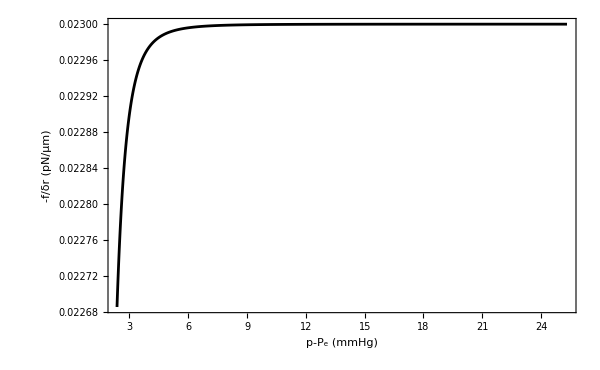

```mathematica
(*--- Plot force ---*)
Size=20;imgSize=600;imagePadding={{100,100},{80,10}};
mshaded=Directive[Lighter[Black,0.65],Opacity[0.3],AbsoluteThickness[2]];
tshaded=Directive[Lighter[Black,0.65],Opacity[0.3],DotDashed,AbsoluteThickness[2]];
bfont=Directive[Size,Black,FontFamily->"Arial"];
fT=Select[fT,Length[#]≠0&];

h1=Show[
(*ListLogPlot[fM[[2;;]],Joined->True,PlotRange->{{0,p2},All},PlotStyle->mshaded],*)
ListPlot[fC[[1]],Joined->True,PlotRange->{{0,p2},All},PlotStyle->mdefault],
PlotRange->All,Frame->True,AxesOrigin->{0,0},BaseStyle->bfont,
FrameLabel->{Style["p-P_e (mmHg)",bfont],Style["-f/δr (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding
]
Export["thickness.pdf",h1];
```

```mathematica
Length[fM]
prova=Select[fM,Length[#]>0&];
Length[prova]
Print[fM[[397;;397]]]
```

500

499

{{{2.14773,-9655.13},{2.16296,-9655.01},{2.17831,-9654.88},{2.19376,-9654.76},{2.20932,-9654.63},{2.225,-9654.5},{2.24078,-9654.37},{2.25668,-9654.25},{2.27269,-9654.12},{2.28881,-9653.98},{2.30505,-9653.85},{2.3214,-9653.72},{2.33787,-9653.59},{2.35445,-9653.45},{2.37116,-9653.32},{2.38798,-9653.18},{2.40492,-9653.04},{2.42198,-9652.91},{2.43916,-9652.77},{2.45646,-9652.63},{2.47389,-9652.49},{2.49144,-9652.35},{2.50912,-9652.2},{2.52692,-9652.06},{2.54484,-9651.92},{2.5629,-9651.77},{2.58108,-9651.63},{2.59939,-9651.48},{2.61783,-9651.33},{2.6364,-9651.18},{2.6551,-9651.03},{2.67394,-9650.88},{2.69291,-9650.73},{2.71201,-9650.58},{2.73125,-9650.43},{2.75063,-9650.27},{2.77014,-9650.12},{2.78979,-9649.96},{2.80959,-9649.8},{2.82952,-9649.65},{2.84959,-9649.49},{2.86981,-9649.33},{2.89016,-9649.17},{2.91067,-9649.},{2.93132,-9648.84},{2.95211,-9648.68},{2.97305,-9648.51},{2.99415,-9648.35},{3.01539,-9648.18},{3.03678,-9648.01},{3.05832,-9647.84},{3.08002,-9647.67},{3.10187,-9647.5},{3.12387,-9647.33},{3.14604,-9647.16},{3.16835,-9646.98},{3.19083,-9646.81},{3.21347,-9646.63},{3.23626,-9646.46},{3.25922,-9646.28},{3.28234,-9646.1},{3.30563,-9645.92},{3.32908,-9645.74},{3.3527,-9645.55},{3.37648,-9645.37},{3.40044,-9645.19},{3.42456,-9645.},{3.44885,-9644.81},{3.47332,-9644.62},{3.49796,-9644.44},{3.52278,-9644.25},{3.54777,-9644.05},{3.57294,-9643.86},{3.59828,-9643.67},{3.62381,-9643.47},{3.64952,-9643.28},{3.67541,-9643.08},{3.70148,-9642.88},{3.72774,-9642.68},{3.75419,-9642.48},{3.78082,-9642.28},{3.80764,-9642.08},{3.83465,-9641.87},{3.86186,-9641.67},{3.88925,-9641.46},{3.91684,-9641.25},{3.94463,-9641.05},{3.97261,-9640.84},{4.0008,-9640.63},{4.02918,-9640.41},{4.05776,-9640.2},{4.08655,-9639.98},{4.11554,-9639.77},{4.14474,-9639.55},{4.17414,-9639.33},{4.20375,-9639.11},{4.23357,-9638.89},{4.26361,-9638.67},{4.29386,-9638.45},{4.32432,-9638.22},{4.35499,-9638.},{4.38589,-9637.77},{4.417,-9637.54},{4.44834,-9637.31},{4.4799,-9637.08},{4.51168,-9636.85},{4.54368,-9636.62},{4.57592,-9636.38},{4.60838,-9636.15},{4.64107,-9635.91},{4.674,-9635.67},{4.70716,-9635.43},{4.74055,-9635.19},{4.77418,-9634.95},{4.80805,-9634.71},{4.84216,-9634.46},{4.87651,-9634.21},{4.9111,-9633.97},{4.94594,-9633.72},{4.98103,-9633.47},{5.01637,-9633.22},{5.05195,-9632.96},{5.08779,-9632.71},{5.12389,-9632.45},{5.16024,-9632.2},{5.19684,-9631.94},{5.23371,-9631.68},{5.27084,-9631.42},{5.30823,-9631.16},{5.34589,-9630.9},{5.38382,-9630.63},{5.42201,-9630.36},{5.46047,-9630.1},{5.49921,-9629.83},{5.53822,-9629.56},{5.57751,-9629.29},{5.61708,-9629.01},{5.65693,-9628.74},{5.69706,-9628.47},{5.73748,-9628.19},{5.77818,-9627.91},{5.81917,-9627.63},{5.86045,-9627.35},{5.90203,-9627.07},{5.9439,-9626.78},{5.98607,-9626.5},{6.02853,-9626.21},{6.0713,-9625.93},{6.11437,-9625.64},{6.15775,-9625.35},{6.20143,-9625.06},{6.24543,-9624.76},{6.28973,-9624.47},{6.33435,-9624.17},{6.37929,-9623.87},{6.42454,-9623.58},{6.47012,-9623.28},{6.51602,-9622.98},{6.56225,-9622.67},{6.6088,-9622.37},{6.65569,-9622.06},{6.7029,-9621.76},{6.75045,-9621.45},{6.79834,-9621.14},{6.84657,-9620.83},{6.89514,-9620.52},{6.94406,-9620.2},{6.99332,-9619.89},{7.04293,-9619.57},{7.0929,-9619.26},{7.14321,-9618.94},{7.19389,-9618.62},{7.24492,-9618.3},{7.29632,-9617.97},{7.34808,-9617.65},{7.40021,-9617.33},{7.45271,-9617.},{7.50558,-9616.67},{7.55883,-9616.34},{7.61245,-9616.01},{7.66645,-9615.68},{7.72084,-9615.35},{7.77561,-9615.01},{7.83078,-9614.68},{7.88633,-9614.34},{7.94228,-9614.},{7.99862,-9613.66},{8.05536,-9613.32},{8.11251,-9612.98},{8.17006,-9612.64},{8.22802,-9612.3},{8.28639,-9611.95},{8.34518,-9611.6},{8.40438,-9611.26},{8.464,-9610.91},{8.52405,-9610.56},{8.58452,-9610.21},{8.64542,-9609.85},{8.70675,-9609.5},{8.76852,-9609.15},{8.83072,-9608.79},{8.89337,-9608.43},{8.95646,-9608.08},{9.02,-9607.72},{9.08399,-9607.36},{9.14843,-9607.},{9.21333,-9606.63},{9.27869,-9606.27},{9.34452,-9605.91},{9.41081,-9605.54},{9.47757,-9605.18},{9.54481,-9604.81},{9.61252,-9604.44},{9.68071,-9604.07},{9.74939,-9603.7},{9.81855,-9603.33},{9.88821,-9602.96},{9.95836,-9602.59},{10.029,-9602.22},{10.1002,-9601.84},{10.1718,-9601.47},{10.244,-9601.09},{10.3166,-9600.71},{10.3898,-9600.34},{10.4635,-9599.96},{10.5378,-9599.58},{10.6125,-9599.2},{10.6878,-9598.82},{10.7636,-9598.44},{10.84,-9598.06},{10.9169,-9597.68},{10.9943,-9597.3},{11.0723,-9596.91},{11.1509,-9596.53},{11.23,-9596.15},{11.3097,-9595.76},{11.3899,-9595.38},{11.4707,-9594.99},{11.5521,-9594.61},{11.634,-9594.22},{11.7165,-9593.84},{11.7997,-9593.45},{11.8834,-9593.06},{11.9677,-9592.68},{12.0526,-9592.29},{12.1381,-9591.9},{12.2242,-9591.52},{12.3109,-9591.13},{12.3983,-9590.74},{12.4862,-9590.35},{12.5748,-9589.97},{12.664,-9589.58},{12.7538,-9589.19},{12.8443,-9588.81},{12.9354,-9588.42},{13.0272,-9588.03},{13.1196,-9587.65},{13.2127,-9587.26},{13.3064,-9586.88},{13.4008,-9586.49},{13.4959,-9586.11},{13.5916,-9585.72},{13.6881,-9585.34},{13.7852,-9584.96},{13.883,-9584.58},{13.9814,-9584.19},{14.0806,-9583.81},{14.1805,-9583.43},{14.2811,-9583.06},{14.3824,-9582.68},{14.4845,-9582.3},{14.5872,-9581.93},{14.6907,-9581.55},{14.7949,-9581.18},{14.8999,-9580.81},{15.0056,-9580.43},{15.112,-9580.06},{15.2192,-9579.7},{15.3272,-9579.33},{15.4359,-9578.96},{15.5454,-9578.6},{15.6557,-9578.24},{15.7668,-9577.88},{15.8786,-9577.52},{15.9913,-9577.16},{16.1047,-9576.81},{16.219,-9576.46},{16.334,-9576.11},{16.4499,-9575.76},{16.5666,-9575.41},{16.6841,-9575.07},{16.8025,-9574.73},{16.9217,-9574.39},{17.0418,-9574.06},{17.1627,-9573.72},{17.2844,-9573.39},{17.407,-9573.07},{17.5305,-9572.74},{17.6549,-9572.42},{17.7801,-9572.1},{17.9063,-9571.79},{18.0333,-9571.48},{18.1612,-9571.17},{18.2901,-9570.86},{18.4198,-9570.56},{18.5505,-9570.27},{18.6821,-9569.97},{18.8146,-9569.68},{18.9481,-9569.4},{19.0825,-9569.12},{19.2179,-9568.84},{19.3542,-9568.57},{19.4915,-9568.3},{19.6298,-9568.04},{19.7691,-9567.78},{19.9093,-9567.53},{20.0506,-9567.28},{20.1928,-9567.04},{20.336,-9566.8},{20.4803,-9566.57},{20.6256,-9566.34},{20.7719,-9566.12},{20.9193,-9565.91},{21.0677,-9565.7},{21.2171,-9565.5},{21.3677,-9565.3},{21.5193,-9565.11}}}